## Morgan Nance Assignment 6 Question 1

## Q1a

```mathematica
(*binding constants given in problem*)
ka1=10^3;
ka2=10^6;
ka3=10^9;
```

```mathematica
(*assuming that the binding spots are not identical but independent*)
xbar[x_]:=(ka1*x/(1+ka1*x))+(ka2*x/(1+ka2*x)) +(ka3*x/(1+ka3*x))
```

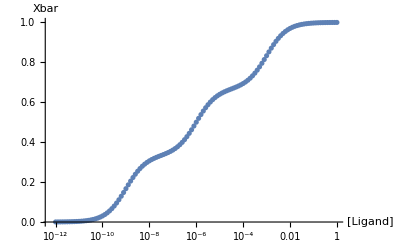

```mathematica
(*ListLinePlot[Table[{x,xbar[10^x]/3},{x,-12,0,0.1}],AxesLabel->{"Concentration 10^x","Xbar"}]*)
(*be fancy and plot the xbar equation using a Log plot from concentrations of 10^-12 to 10^0*)
q1aplot=ListLogLinearPlot[Table[{10^x,xbar[10^x]/3},{x,-12,0,0.1}],AxesLabel->{"[Ligand]","Xbar"}]
```

```mathematica
(*now fit the xbar equation and see if you can get the right Ka values back*)
(*generate data using the xbar equation to use to fit an equation to*)
xbardata=Table[{x,xbar[10^x]},{x,-12,0,0.1}];
```

```mathematica
(*fit the data to an equation*)
q1anlm=NonlinearModelFit[xbardata,(ka1fit*10^x/(1+ka1fit*10^x))+(ka2fit*10^x/(1+ka2fit*10^x)) +(ka3fit*10^x/(1+ka3fit*10^x)),{ka1fit,ka2fit,ka3fit},x];
(*I am able to get back the appropriate Ka terms. Error is very low (see ParameterTable)*)
q1anlm["BestFitParameters"]
q1anlm["ParameterTable"]
```

{ka1fit→1000.,ka2fit→1.×10^9,ka3fit→1.×10^6}

| Estimate | Standard Error | t-Statistic | P-Value
ka1fit | 1000. | 2.47973×10^-13 | 4.0327×10^15 | 4.423923719529×10^-1721
ka2fit | 1.×10^9 | 2.47973×10^-7 | 4.0327×10^15 | 4.423923719529×10^-1721
ka3fit | 1.×10^6 | 2.48081×10^-10 | 4.03094×10^15 | 4.65789790114165×10^-1721

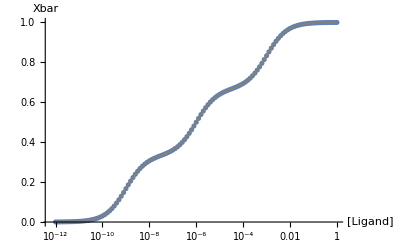

```mathematica
(*the NonlinearModelFit and the data overlap perfectly*)
Show[q1aplot,ListLogLinearPlot[Table[{10^x,q1anlm[x]/3},{x,-12,0,0.1}],Joined->True,PlotStyle->Gray]]
```

```mathematica
Q1b
```

```mathematica
(*add 1% and 5% error to the xbar data*)
xbardata1error=Transpose[{xbardata[[All,1]],xbardata[[All,2]]+RandomVariate[NormalDistribution[0,0.01],Length[xbardata]]}];
xbardata5error=Transpose[{xbardata[[All,1]],xbardata[[All,2]]+RandomVariate[NormalDistribution[0,0.05],Length[xbardata]]}];
```

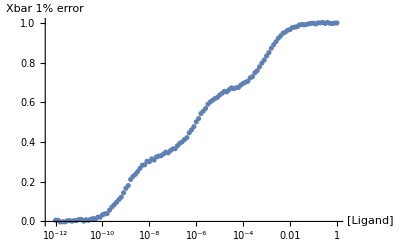

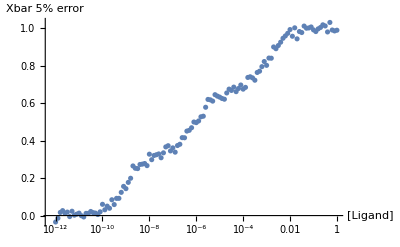

```mathematica
(*plot the data with 1% and 5% error*)
xydata=Transpose[{10^xbardata1error[[All,1]],xbardata1error[[All,2]]/3}];
q1bplot1error=ListLogLinearPlot[xydata,AxesLabel->{"[Ligand]","Xbar 1% error"}]

xydata=Transpose[{10^xbardata5error[[All,1]],xbardata5error[[All,2]]/3}];
q1bplot5error=ListLogLinearPlot[xydata,AxesLabel->{"[Ligand]","Xbar 5% error"}]
```

```mathematica
(*Can we get the right Ka values with the error-filled data?*)
```

{ka1fit→996.722,ka2fit→997626.,ka3fit→9.92947×10^8}

| Estimate | Standard Error | t-Statistic | P-Value
ka1fit | 996.722 | 11.9146 | 83.6558 | 6.70985×10^-107
ka2fit | 997626. | 11930.6 | 83.619 | 7.06145×10^-107
ka3fit | 9.92947×10^8 | 1.18695×10^7 | 83.6555 | 6.71291×10^-107

1% error gives back good Ka values

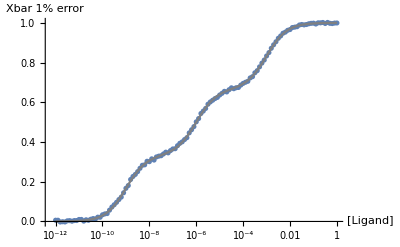

```mathematica
(*fit the 1% error data to an equation*)
q1b1errornlm=NonlinearModelFit[xbardata1error,(ka1fit*10^x/(1+ka1fit*10^x))+(ka2fit*10^x/(1+ka2fit*10^x)) +(ka3fit*10^x/(1+ka3fit*10^x)),{ka1fit,ka2fit,ka3fit},x];
q1b1errornlm["BestFitParameters"]
q1b1errornlm["ParameterTable"]
Print["1% error gives back good Ka values"]
Show[q1bplot1error,ListLogLinearPlot[Table[{10^x,q1b1errornlm[x]/3},{x,-12,0,0.1}],Joined->True,PlotStyle->Gray]]
```

{ka1fit→928.572,ka2fit→9.69935×10^8,ka3fit→1.05073×10^6}

| Estimate | Standard Error | t-Statistic | P-Value
ka1fit | 928.572 | 53.1882 | 17.4582 | 1.71579×10^-34
ka2fit | 9.69935×10^8 | 5.55652×10^7 | 17.4558 | 1.73619×10^-34
ka3fit | 1.05073×10^6 | 60215.5 | 17.4496 | 1.79003×10^-34

5% error gives back error-prone Ka values

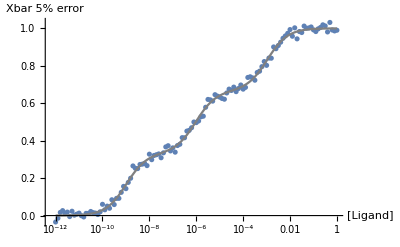

```mathematica
(*fit the 5% error data to an equation*)
q1b5errornlm=NonlinearModelFit[xbardata5error,(ka1fit*10^x/(1+ka1fit*10^x))+(ka2fit*10^x/(1+ka2fit*10^x)) +(ka3fit*10^x/(1+ka3fit*10^x)),{ka1fit,ka2fit,ka3fit},x];
q1b5errornlm["BestFitParameters"]
q1b5errornlm["ParameterTable"]
Print["5% error gives back error-prone Ka values"]
Show[q1bplot5error,ListLogLinearPlot[Table[{10^x,q1b5errornlm[x]/3},{x,-12,0,0.1}],Joined->True,PlotStyle->Gray]]
```

```mathematica
Q1c
```

```mathematica
(*binding constants given in problem*)
q1cka1=10^6;
q1cka2=10^5.5;
q1cka3=10^6.5;
q1cxbar[x_]:=(q1cka1*x/(1+q1cka1*x))+(q1cka2*x/(1+q1cka2*x)) +(q1cka3*x/(1+q1cka3*x))
```

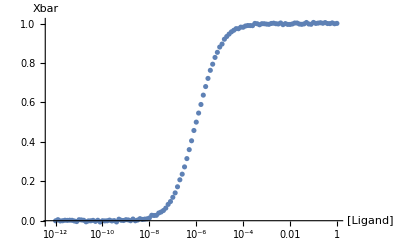

```mathematica
(*add 1% error to the Xbar data again*)
q1cxbardata = Table[{x,q1cxbar[10^x]},{x,-12,0,0.1}];
q1cxbardata1error=Transpose[{q1cxbardata[[All,1]],q1cxbardata[[All,2]]+RandomVariate[NormalDistribution[0,0.01],Length[q1cxbardata]]}];

(*Plot*)
xydata=Transpose[{10^q1cxbardata1error[[All,1]],q1cxbardata1error[[All,2]]/3}];
q1cplot=ListLogLinearPlot[xydata,AxesLabel->{"[Ligand]","Xbar"}]
```

{ka1fit→998370.,ka2fit→316775.,ka3fit→3.11931×10^6}

| Estimate | Standard Error | t-Statistic | P-Value
ka1fit | 998370. | 54379.9 | 18.3592 | 2.2084×10^-36
ka2fit | 316775. | 10326.7 | 30.6754 | 4.60256×10^-58
ka3fit | 3.11931×10^6 | 102359. | 30.4742 | 9.17647×10^-58

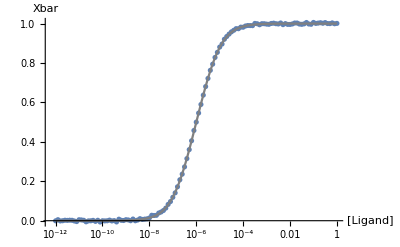

```mathematica
(*fit the 1% error data to an equation*)
q1c1errornlm=NonlinearModelFit[q1cxbardata1error,(ka1fit*10^x/(1+ka1fit*10^x))+(ka2fit*10^x/(1+ka2fit*10^x)) +(ka3fit*10^x/(1+ka3fit*10^x)),{ka1fit,ka2fit,ka3fit},x];
q1c1errornlm["BestFitParameters"]
q1c1errornlm["ParameterTable"]
Show[q1cplot,ListLogLinearPlot[Table[{10^x,q1c1errornlm[x]/3},{x,-12,0,0.1}],Joined->True,PlotStyle->Gray]]
```

```mathematica
It seems like it is difficult to resolve binding parameters when there is more than one binding location since my error is high, but my models fit the data well. So there's either my own user error, or I missed the point of this question
```